```mathematica
f[x_]:=x^3-4*x-9;
(Label[1];
a=Input["Enter the left end point"];
b=Input["Enter the right end point"];
If[f[a]*f[b]>0,{Print["Enter a and b suchthat f[a] and f[b] have opposite sign"];
Goto[1];}];);
n=Input["Enter maximum number of iteration"];
tol=Input["Enter tolerence"];
Print["Iteration------A----B---C---Error"];
k=0;
For[i=1,i≤n,i++,{
x0[i]=a;
x1[i]=b;
c=(a+b)/2;
x2[i]=c;
k++;
If[(f[c]==0||Abs[a-b]≤tol),Break[];,
If[f[c]*f[a]>0,a=c,b=c];]}
];
t=Table[{i,x0[i],x1[i],x2[i],f[x2[i]]},{i,1,k}];
PaddedForm[TableForm[t]//N,{10,7}]
If[k==n,Print["Maximum number of iteration exceeded"]]
```

Iteration------A----B---C---Error

1.0000000 |    1.0000000 |    3.0000000 |    2.0000000 |   -9.0000000
   2.0000000 |    2.0000000 |    3.0000000 |    2.5000000 |   -3.3750000
   3.0000000 |    2.5000000 |    3.0000000 |    2.7500000 |    0.7968750
   4.0000000 |    2.5000000 |    2.7500000 |    2.6250000 |   -1.4121094
   5.0000000 |    2.6250000 |    2.7500000 |    2.6875000 |   -0.3391113
   6.0000000 |    2.6875000 |    2.7500000 |    2.7187500 |    0.2209167
   7.0000000 |    2.6875000 |    2.7187500 |    2.7031250 |   -0.0610771
   8.0000000 |    2.7031250 |    2.7187500 |    2.7109375 |    0.0794234
   9.0000000 |    2.7031250 |    2.7109375 |    2.7070313 |    0.0090492
  10.0000000 |    2.7031250 |    2.7070313 |    2.7050781 |   -0.0260449
  11.0000000 |    2.7050781 |    2.7070313 |    2.7060547 |   -0.0085056
  12.0000000 |    2.7060547 |    2.7070313 |    2.7065430 |    0.0002699

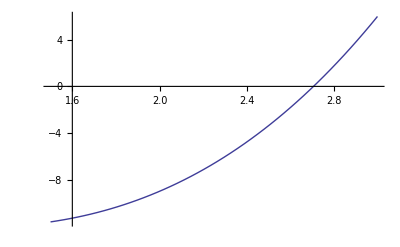

```mathematica
Plot[x^3-4x-9,{x,1.5,3}]
```